```mathematica
ClearAll["Global*`"]
```

```mathematica
(*Problem 1*)
ClearAll[x,f];
f[x_]:=ⅇ^Sin[x+c];
Solve[f'[x]==0&&f''[x]<0,{x},Reals]/.C[1]->0
```

{{x→-c+π/2}}

```mathematica
(*Problem 2*)
ClearAll[γ,a]
aij[n_,m_]:=If[n==m,(n^4+γ)π^2-2*a((n^2*π^2)/3-1),16*a*(m*n(m^2+n^2))/((m^2-n^2)^2)];
matrixMaker[K_]:=Table[aij[n,m],{n,1,K,2},{m,1,K,2}]
a3=a/.Solve[Det[matrixMaker[3]]==0,a]//FullSimplify;
a1=a/.Solve[Det[matrixMaker[1]]==0,a]//FullSimplify;
solutions={a1[[1]],a3[[1]],a3[[2]]};
TableForm[solutions,TableHeadings->{{"α_1(γ)","α_2(γ)","α_3(γ)"},{}}]
```

α_1(γ) | (3 π^2 (1+γ))/(2 (-3+π^2))
α_2(γ) | (2 π^2 (20 π^2 (9+γ)-12 (41+γ)-√(15360 π^2 (-9+γ)+256 π^4 (-9+γ)^2+225 (1753+9 γ (82+γ)))))/(-627-160 π^2+48 π^4)
α_3(γ) | (2 π^2 (20 π^2 (9+γ)-12 (41+γ)+√(15360 π^2 (-9+γ)+256 π^4 (-9+γ)^2+225 (1753+9 γ (82+γ)))))/(-627-160 π^2+48 π^4)

```mathematica
(*gamma = 0*)
γ=0;
aij2[n_,m_]:=If[n==m,(n^4+γ)π^2-2*a((n^2*π^2)/3-1),16*a*(m*n(m^2+n^2))/((m^2-n^2)^2)];
matrixMaker2[K_]:=Table[aij[n,m],{n,1,K,2},{m,1,K,2}];
a0=Table[a/.NSolve[Det[matrixMaker[x]]==0,a][[1]],{x,{1,3,5}}];
(*gamma = 0.4*)
γ=0.4;
aij2[n_,m_]:=If[n==m,(n^4+γ)π^2-2*a((n^2*π^2)/3-1),16*a*(m*n(m^2+n^2))/((m^2-n^2)^2)];
matrixMaker2[K_]:=Table[aij[n,m],{n,1,K,2},{m,1,K,2}];
a4=Table[a/.NSolve[Det[matrixMaker[x]]==0,a][[1]],{x,{1,3,5}}];
TableForm[{a0,a4}//Transpose,TableHeadings->{{"K=1","K=3","K=5"},{"γ=0","γ=0.4"}}]
```

| γ=0 | γ=0.4
K=1 | 2.15506 | 3.01708
K=3 | 2.07719 | 2.86004
K=5 | 2.07595 | 2.85824

```mathematica
(* test *)
(*Table[aij[n,m],{n,1,2},{m,1,2}]//MatrixForm

tbl=Table[aij[n,m],{n,1,3,2},{m,1,3,2}];
MatrixForm[tbl]
dd=Det[tbl]
Solve[dd==0,a]//FullSimplify*)
```

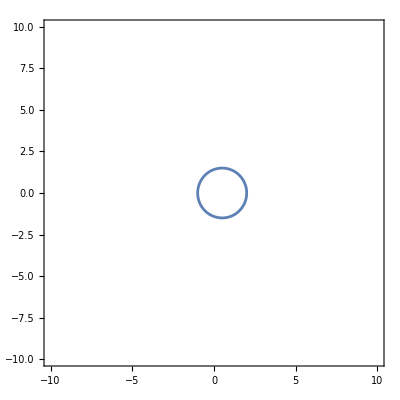

-Graphics3D-

```mathematica
(*Problem 3*)
(*Visualize volume of intersection *)
(*Plots*)
ContourPlot[4-x^2-y^2==(2-x),{x,-10,10},{y,-10,10}]
Plot3D[{4-x^2-y^2,2-x},{y,-10,10},{x,-10,10}]
(*RegionPlot3D[{4-x^2-y^2>z&&2-x>z},{x,-5,5},{y,-5,5},{z,-5,5}]*)
(*Note: z2 is bottom*)
```

```mathematica
ClearAll[x,y]
z1=4-x^2-y^2;
z2=2-x;
R=ImplicitRegion[z1>=z2,{{x,-2,2},{y,-2,2}}];
result=Integrate[z1-z2,{x,y}∈R];
Print["The volume of the body of intersection is:", result]
```

The volume of the body of intersection is:(81 π)/32

```mathematica
(*Problem 4*)
eq=y''''[x]+(2/x)*y'''[x]-(1/x^2)*y''[x]+(1/x^3)*y'[x]==1;
boundIn={y[a]==0,y'[a]==0};
boundOut={(y''[x]+(v/x)*y'[x])==0,(y'''[x]+(1/x)*y''[x]-(1/x^2)*y'[x])==0}/.x->1;
result=Flatten[DSolve[{eq,boundIn,boundOut},y[x],x]][[1,2]]/.x->z;
```

```mathematica
a=0.2;v=0.3;
soln=NDSolve[{eq,boundIn,boundOut},y,{x,a,1}];
```

```mathematica
plt={Plot[Evaluate[y[x]/.soln],{x,a,1},AxesLabel->{"z","y(z)"}],
Plot[Evaluate[y'[x]/.soln],{x,a,1},AxesLabel->{"z","y(z)"}],
Plot[Evaluate[y''[x]/.soln],{x,a,1},AxesLabel->{"z","y(z)"}],
Plot[Evaluate[y'''[x]/.soln],{x,a,1},AxesLabel->{"z","y(z)"}]};
```

the solution of the given differential equation is:
1/(64 (a^2 v-a^2-v-1))(a^6 v-a^6-2 a^4 v z^2+4 a^4 v log(z)-3 a^4 v-4 a^4 v log(a)+2 a^4 z^2+4 a^4 log(z)+5 a^4-4 a^4 log(a)+a^2 v z^4+4 a^2 v z^2+8 a^2 v z^2 log(a)-8 a^2 v z^2 log(z)-4 a^2 v log(z)-16 a^2 v log(a) log(z)+2 a^2 v+16 a^2 v log^2(a)-4 a^2 v log(a)-a^2 z^4-4 a^2 z^2-8 a^2 z^2 log(a)+8 a^2 z^2 log(z)-16 a^2 log(a) log(z)+4 a^2 log(z)+6 a^2+16 a^2 log^2(a)-12 a^2 log(a)-v z^4-2 v z^2+8 v z^2 log(z)-z^4-6 z^2+8 z^2 log(z))

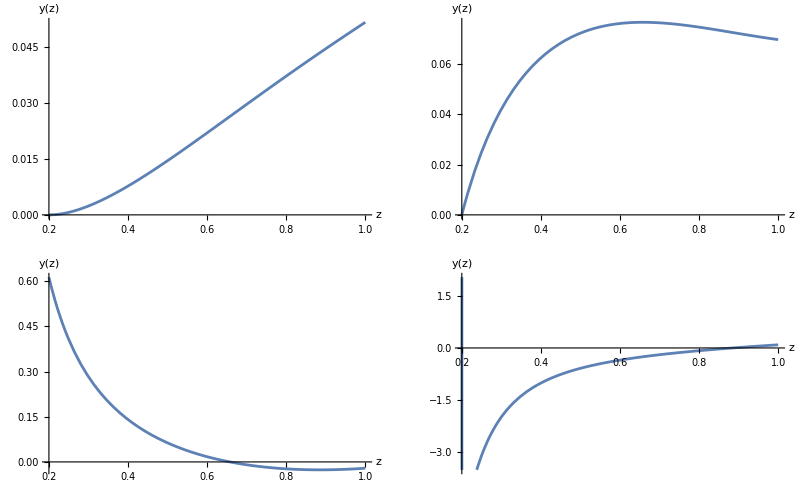

```mathematica
ClearAll[a,v]
Print["the solution of the given differential equation is:\n",result//TraditionalForm]
GraphicsGrid[Partition[plt,2]]
```

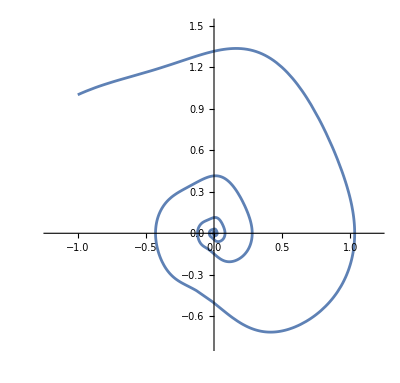

```mathematica
(*Problem 5*)
ϵ=0.16;
γ=0.4;
w=0.97;
L=1+ϵ*w*(Sin[w*t+9*π/8])^7;
dlt=7*ϵ*(Sin[w*t+9*π/8])^6*Cos[w*t+9π/8];
eq1=y1'[t]==y2[t];
eq2=y2'[t]==-(2/L*dlt+γ*L)*y2[t]-1/L*Sin[y1[t]];
sol=NDSolve[{eq1,eq2,y1[0]==-1,y2[0]==1},{y1[t],y2[t]},{t,0,50}];
ParametricPlot[Evaluate[{y1[t],y2[t]}/.sol],{t,0,50},PlotRange->{{-1.2,1.2},{-.8,1.5}}]
```

```mathematica
(*Problem 6*)
ClearAll[mod,J,θ,η,s,L,p0]

deflection={θ''[s] + p0*Sin[θ[s]]==0,θ[0]==a,θ'[0]==-π};
theta=ParametricNDSolve[deflection,θ,{s,0,1},{p0,a}]
```

{θ→ParametricFunction[<>]}

```mathematica
phi[p0_,a_]:=(θ[p0,a]/.theta)[s]-(θ[p0,a]/.theta)[1]
x=Table[Table[NIntegrate[Cos[phi[p0,π/2]],{s,b,1}],{b,0,1,0.01}],{p0,{0.02,15,25,35}}];
y=Table[Table[NIntegrate[Sin[phi[p0,π/2]],{s,b,1}],{b,0,1,0.01}],{p0,{0.02,15,25,35}}];
```

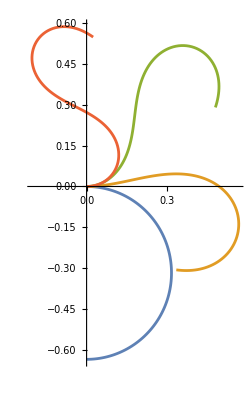

```mathematica
ListLinePlot[Table[Transpose[{x[[p]],-y[[p]]}],{p,1,4}],AspectRatio->Automatic]
```

```mathematica
x2=Table[Table[NIntegrate[Cos[phi[p0,0]],{s,b,1}],{b,0,1,0.01}],{p0,{0.02,3,9,12}}];
y2=Table[Table[NIntegrate[Sin[phi[p0,0]],{s,b,1}],{b,0,1,0.01}],{p0,{0.02,3,9,12}}];
```

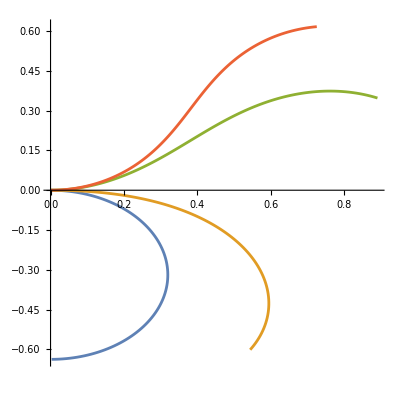

```mathematica
ListLinePlot[Table[Transpose[{x2[[p]],-y2[[p]]}],{p,1,4}],AspectRatio->1]
```

```mathematica
(*Problem 7*)
ClearAll[θ,x,nθ]
n0=NDSolveValue[{θ''[x]+2/x*θ'[x]+1==0,θ[0.001]==1,θ'[0.001]==0},θ[x],{x,0.001,6}];
nRoot0= FindRoot[n0,{x,3}]
(*Plot[n0,{x,0.001,6},PlotRange->All]*)
```

{x→2.44949}

```mathematica
n1=NDSolveValue[{θ''[x]+2/x*θ'[x]+θ[x]^1==0,θ[0.001]==1,θ'[0.001]==0},θ[x],{x,0.001,6}];
nRoot1= FindRoot[n1,{x,3}]
```

{x→3.14159}

```mathematica
n2=NDSolveValue[{θ''[x]+2/x*θ'[x]+θ[x]^2==0,θ[0.001]==1,θ'[0.001]==0},θ[x],{x,2,6}];
nRoot2= FindRoot[n2,{x,3}]
```

{x→4.35287}

```mathematica
θ0[x]=1-x^2/6;
θ1[x]=Sin[x]/x;
aRoot0=FindRoot[θ0[x],{x,3}];
aRoot1=FindRoot[θ1[x],{x,3}];
```

```mathematica
diff0=(x/.nRoot0)-(x/.aRoot0);
diff1=(x/.nRoot1)-(x/.aRoot1);
```

```mathematica
n0={x/.nRoot0,x/.aRoot0,diff0};
n1={x/.nRoot1,x/.aRoot1,diff1};
n2={x/.nRoot2,"-","-"};
TableForm[{n0,n1,n2}//Transpose,TableHeadings->{{"NumericalRoots", "AnalyticalRoots","Difference"},{"n = 0", "n = 1", "n = 2"}}]
```

| n = 0 | n = 1 | n = 2
NumericalRoots | 2.44949 | 3.14159 | 4.35287
AnalyticalRoots | 2.44949 | 3.14159 | -
Difference | 6.12054×10^-7 | 6.98387×10^-8 | -

```mathematica
n02=NDSolveValue[{θ''[x]+2/x*θ'[x]+1==0,θ[0.001]==1,θ'[0.001]==1},θ[x],{x,0.001,6}];
nRoot02= FindRoot[n02,{x,3}]
n12=NDSolveValue[{θ''[x]+2/x*θ'[x]+θ[x]^1==0,θ[0.001]==1,θ'[0.001]==1},θ[x],{x,0.001,6}];
nRoot12= FindRoot[n12,{x,3}]
n22=NDSolveValue[{θ''[x]+2/x*θ'[x]+θ[x]^2==0,θ[0.001]==1,θ'[0.001]==1},θ[x],{x,0.001,6}];
nRoot22= FindRoot[n22,{x,3}]
```

{x→2.45071}

{x→3.14159}

{x→4.3507}

```mathematica
diff02=(x/.nRoot02)-(x/.aRoot0);
diff12=(x/.nRoot12)-(x/.aRoot1);
n02={x/.nRoot02,x/.aRoot0,diff02};
n12={x/.nRoot12,x/.aRoot1,diff12};
n22={x/.nRoot22,"-","-"};
TableForm[{n02,n12,n22}//Transpose,TableHeadings->{{"NumericalRoots", "AnalyticalRoots","Difference"},{"n = 0", "n = 1", "n = 2"}}]
```

| n = 0 | n = 1 | n = 2
NumericalRoots | 2.45071 | 3.14159 | 4.3507
AnalyticalRoots | 2.44949 | 3.14159 | -
Difference | 0.00122455 | 1.08413×10^-6 | -

```mathematica
(*Problem 8 EC*)
Framed[Manipulate[Grid[{{Graphics[{Circle[{0,0},1],Blue,PointSize[0.05],Point[{Cos[θ],Sin[θ]}]},ImageSize->{200,200},Axes->True],Plot[Sin[theta],{theta,0,2π},Epilog->{Blue,PointSize[0.03],Point[{θ,Sin[θ]}],Line[{{θ,0},{θ,Sin[θ]}}]},ImageSize->{400,200}]}},Frame->All,FrameStyle->Thick],{θ,0,2π}]]
```